# MixedChinesePostmanProblem

One-line description explaining the function’s basic purpose

## Definition

```mathematica
ClearAll[FindMixedPostmanTour]
FindMixedPostmanTour[g_?MixedGraphQ]:=Block[{
	une,de,
	unX,
	unrevX,
	dX,
	vlist,
	c412,
	elist,
	res,
	edges
},
	une=EdgeList[g,_UndirectedEdge];
	de=EdgeList[g,_DirectedEdge];

	unX=und@@@une;
	unrevX=Reverse/@unX;


	dX=d@@@de;
	vlist=VertexList[g];
	c412=
		Total[
			Flatten[{Cases[dX, d[#,_]], -Cases[dX, d[_,#]]}]
		]+Total[
			Cases[unX, und[#,_]|und[_,#]]
			-Reverse/@Cases[unX, und[#,_]|und[_,#]]
		]&/@vlist;


	elist=Flatten[{unX,unrevX,dX}];
	res=LinearOptimization[
		(Total[unX+unrevX]+Total[dX]),
		{
			(*4.11*)
			unX+unrevX\[VectorGreaterEqual]1,

			(*4.12*)(*a.u+b.v\[VectorLessEqual]1,a.v+b.u\[VectorLessEqual]1,*)
			c412==0,

			(*4.13*)
			dX\[VectorGreaterEqual]1,

			(*4.14*)
			unX\[VectorGreaterEqual]0,
			unrevX\[VectorGreaterEqual]0
		},
		Element[#,Integers]&/@elist
	];

	edges=Flatten[
		If[#[[2]]>0,Table[#[[1]],{#[[2]]}],Nothing]&/@res
	]/.{und->UndirectedEdge,d->DirectedEdge}
]
```

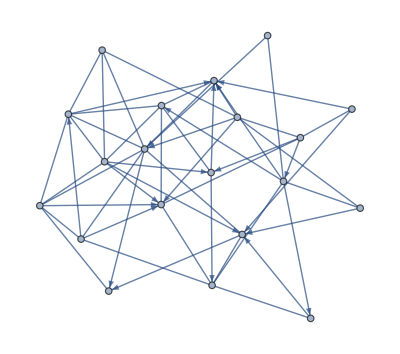

```mathematica
randomGraph=RandomMixedGraph[{20,54},0.68]
```

```mathematica
FindMixedPostmanTour[randomGraph]
```

{2<->20,2<->20,2<->20,2<->20,3<->17,11<->13,12<->16,12<->16,12<->16,13<->17,13<->18,13<->18,15<->17,15<->17,15<->19,15<->19,15<->19,15<->19,15<->19,15<->19,2<->1,15<->1,15<->1,15<->1,15<->1,15<->1,8<->2,8<->2,10<->2,16<->2,6<->3,14<->3,14<->3,7<->4,7<->4,7<->4,7<->4,16<->8,15<->10,13<->11,1->5,1->5,1->17,1->12,1->10,1->18,2->17,3->5,3->7,4->18,4->6,4->6,4->6,5->13,5->19,5->15,6->16,6->17,6->12,6->19,7->11,7->9,7->15,7->19,7->13,8->10,8->17,8->13,9->16,10->19,10->12,10->16,10->16,11->18,14->18,14->19,16->20,16->18,16->19,18->20,18->20,18->20}

```mathematica
MixedGraphToDigraph[randomGraph]
```

-Graphics-

```mathematica
EulerianGraphQ[MixedGraphToDigraph[randomGraph]]
```

False

```mathematica
MixedGraphToDigraph[Graph[FindMixedPostmanTour[randomGraph]]]
```

-Graphics-

```mathematica
GraphSum[MixedGraphToDigraph[Graph[FindMixedPostmanTour[randomGraph]]],MixedGraphToDigraph[randomGraph]]
```

-Graphics-

```mathematica
EulerianGraphQ[MixedGraphToDigraph[Graph[FindMixedPostmanTour[randomGraph]]]]
```

False

```mathematica
FindMixedPostmanTour[randomGraph]
```

{2<->20,2<->20,2<->20,2<->20,3<->17,11<->13,12<->16,12<->16,12<->16,13<->17,13<->18,13<->18,15<->17,15<->17,15<->19,15<->19,15<->19,15<->19,15<->19,15<->19,2<->1,15<->1,15<->1,15<->1,15<->1,15<->1,8<->2,8<->2,10<->2,16<->2,6<->3,14<->3,14<->3,7<->4,7<->4,7<->4,7<->4,16<->8,15<->10,13<->11,1->5,1->5,1->17,1->12,1->10,1->18,2->17,3->5,3->7,4->18,4->6,4->6,4->6,5->13,5->19,5->15,6->16,6->17,6->12,6->19,7->11,7->9,7->15,7->19,7->13,8->10,8->17,8->13,9->16,10->19,10->12,10->16,10->16,11->18,14->18,14->19,16->20,16->18,16->19,18->20,18->20,18->20}

```mathematica
Names["*Path*"]
```

{AddOnHelpPath,AnglePath,AnglePath3D,AutoloadPath,CharacterEncodingsPath,ConfigurationPath,ControllerPath,ConvertersPath,DocumentationPathConfiguration,FindCurvePath,FindEdgeIndependentPaths,FindFileOnPath,FindHamiltonianPath,FindPath,FindShortestPath,FindVertexIndependentPaths,GeoPath,ListCurvePathPlot,NotebookPath,PalettePath,Path,PathGraph,PathGraphQ,PreferencesPath,PrivatePaths,ResourceSystemPath,ShortestPathFunction,SpellingDictionariesPath,StyleSheetPath,SystemHelpPath,$CGPPath,$ContextPath,$DefaultFileBrowserPath,$DefaultPath,$DocumentationPath,$LibraryPath,$Path,$PathnameSeparator,$PersistencePath,$RefGuidePath,$ResourceSystemPath,$TemplatePath}

## Documentation

### Usage

MyFunction[arg]

explanation of what use of the argument arg does.

### Details & Options

Additional information about usage and options.

## Examples

### Basic Examples

Text about the example:

```mathematica
MyFunction[x,y]
```

x y

### Scope

Text about additional examples expanding scope (and see other sections for options, applications, etc):

```mathematica
MyFunction[x,y,z]
```

x y z

### Options

### Applications

### Properties and Relations

### Possible Issues

### Neat Examples

## Source & Additional Information

### Contributed By

Author Name

### Keywords

keyword 1

### Categories

Cloud & Deployment
 Data Manipulation & Analysis
 External Interfaces & Connections
 Geographic Data & Computation
 Graphs & Networks
 Images
 Knowledge Representation & Natural Language
 Notebook Documents & Presentation
 Repository Tools
 Social, Cultural & Linguistic Data
 Strings & Text
 System Operation & Setup
 User Interface Construction
 Wolfram Physics Project |  Core Language & Structure
 Engineering Data & Computation
 Financial Data & Computation
 Geometry
 Higher Mathematical Computation
 Just For Fun
 Machine Learning
 Programming Utilities
 Scientific and Medical Data & Computation
 Sound & Video
 Symbolic & Numeric Computation
 Time-Related Computation
 Visualization & Graphics

### Related Symbols

SymbolName (documented Wolfram Language symbol)

### Related Resource Objects

Resource Name (resources from any Wolfram repository)

### Source/Reference Citation

Source, reference or citation information

### Links

Link to other related material

### Tests

```mathematica
MyFunction[x,y]
```

x y

### Compatibility

#### Wolfram Language Version

13.0+

#### Operating System

Windows |  Mac |  Unix

#### Required Features

Notebooks |  Parallel Kernels |  Cloud Access

#### Environments

SessionLocal or cloud interactive session
 WebEvaluationCloud evaluation initiated by an HTTP request
 BatchJobRemote batch job |  ScriptScript run in batch mode
 WebAPIAPI called through an HTTP request
 |  SubkernelParallel or grid subkernel
 ScheduledScheduled task

#### Cloud Support

Supported in cloud

## Author Notes

Additional information about limitations, issues, etc.

## Submission Notes

Additional information for the reviewer.